```mathematica
D[A0/(1+Exp[A1/A0*r/(a-A2)]),r]
```

-(A1 ⅇ^((A1 r)/(A0 (a-A2))))/((a-A2) (1+ⅇ^((A1 r)/(A0 (a-A2))))^2)

```mathematica
a=1;
A0=4.56;
A1=28.88;
A2=1.36;
B0=1;
B1=3.57;
B2=2.36;
n = 20;
```

```mathematica
u=(a/r)^n+A0/(1+Exp[A1/A0*(r/a-A2)])-B0/(1+Exp[B1/B0*(r/a-B2)]);
f=-D[u,r];
```

```mathematica
f
```

(A1 ⅇ^((A1 (-A2+r/a))/A0))/(a (1+ⅇ^((A1 (-A2+r/a))/A0))^2)-(B1 ⅇ^((B1 (-B2+r/a))/B0))/(a (1+ⅇ^((B1 (-B2+r/a))/B0))^2)+(a n (a/r)^(-1+n))/r^2

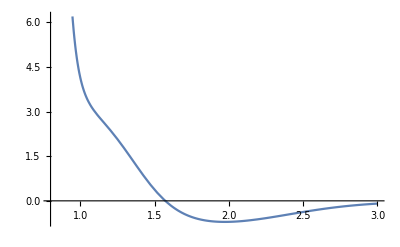

```mathematica
Plot[u,{r,0.8,3}]
```

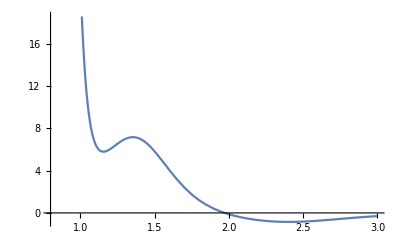

```mathematica
Plot[f,{r,0.8,3}]
```

```mathematica
Manipulate[
Plot[(a/r)^12+A0/(1+Exp[A1/A0*r/(a-A2)])-B0/(1+Exp[B1/B0*r/(a-B2)]),{r,0.8,2}],
{{a,0.9},0,1},{{A0,0.5},0,1},{{A1,0.5},0,1},{{A2,0.5},0,1},{{B0,0.9},0,1},{{B1,0.5},0,1},{{B2,0.5},0,1}
]
```